```mathematica
D[Log[c/Cosh[a]],a]
```

-Tanh[a]

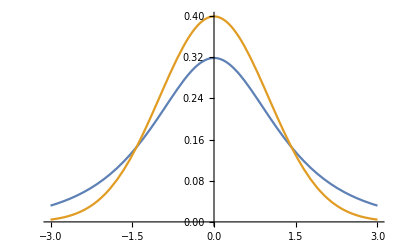

```mathematica
Plot[{1/3.1414110538708586 1/Cosh[a],PDF[NormalDistribution[0,1],a]}, {a,-3,3}]
```

```mathematica
G=({{3/4, 1/2}, {1/2, 1}})
```

{{3/4,1/2},{1/2,1}}

```mathematica
Inverse[G]
```

```mathematica
W = {{2,-1},{-1,3/2}}
```

{{2,-1},{-1,3/2}}

```mathematica
G2=W;
```

```mathematica
W2 = G;
```

```mathematica
ax = 2i -j;ay = -i+3/2 j;
```

```mathematica
zx = -Tanh[2i -j];zy= -Tanh[-i+3/2 j];
```

```mathematica
px = 1/Cosh[2i -j];py= 1/Cosh[-i+3/2 j];
```

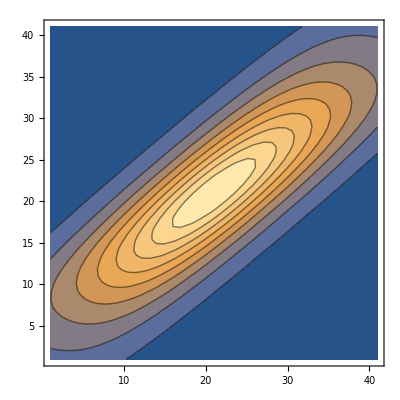

```mathematica
ListContourPlot[Table[1/Cosh[2i -j] 1/Cosh[-i+3/2 j], {i,-2,2,0.1},  {j,-2,2,0.1}]]
```

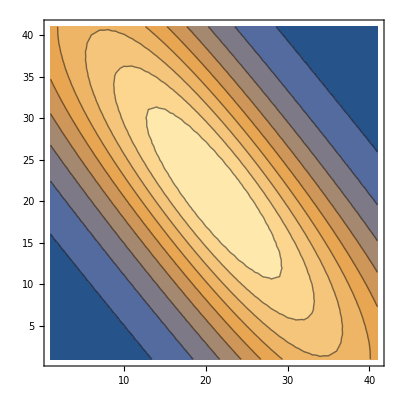

```mathematica
ListContourPlot[Table[1/Cosh[3/4 i +1/2 j] 1/Cosh[1/2 i+j], {i,-2,2,0.1},  {j,-2,2,0.1}]]
```

```mathematica
1/Cosh[0]
```

1

```mathematica
Clear[x]
```

```mathematica
PDF[CauchyDistribution[0,b],x]
```

1/(b π (1+x^2/b^2))

```mathematica
PDF[CauchyDistribution[0,1/π],x]
```

```mathematica
f1 = PDF[CauchyDistribution[0,1/π],2i -j]PDF[CauchyDistribution[0,1/π],-i+3/2 j];
```

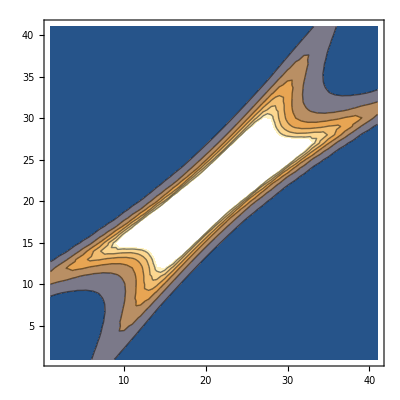

```mathematica
ListContourPlot[Table[f1, {i,-2,2,0.1},  {j,-2,2,0.1}]]
```

```mathematica
f2 = PDF[CauchyDistribution[0,1/π],3/4 i +1/2 j]PDF[CauchyDistribution[0,1/π],1/2 i+j];
```

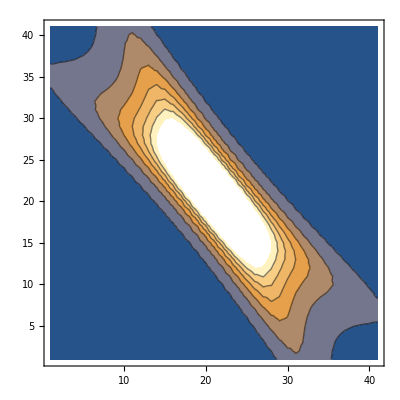

```mathematica
ListContourPlot[Table[f2, {i,-2,2,0.1},  {j,-2,2,0.1}]]
```

```mathematica
NIntegrate[1/Cosh[x], {x,-10,10}]
```

```mathematica
3.1414110538708586
```

3.14141

```mathematica
NIntegrate[PDF[CauchyDistribution[0,1],x], {x,0.01,10}]
```

0.465091

```mathematica
b
```

b

```mathematica
∫_0^∞ PDF[CauchyDistribution[0,b],x]ⅆx
```

ConditionalExpression[1/2 √(1/b^2) b,Im[b^2]≠0||Re[b^2]≥0]